### Proof of Proposition 3.2.10

```mathematica
ClearAll["Global`*"];

(* Smooth convex interpolation inequalities *)
ineqsmooth[x_,y_,gx_,gy_,fx_,fy_]:=-fy+(fx+gx*(y-x)+1/(2L) (gx-gy)^2) (*... ≤0*)
```

```mathematica
x[N+1] = x[N] - λ gradf[N]; (* updates *)
gradf[star] = 0; (* optimality condition *)

ineq1 = ineqsmooth[x[N],x[star],gradf[N],gradf[star],f[N],f[star]];
ineq2 = ineqsmooth[x[N+1],x[N],gradf[N+1],gradf[N],f[N+1],f[N]];

obj  = (x[N+1]-x[star])^2+ (t[N]+2 λ)(f[N+1]-f[star]) - (x[N]-x[star])^2 - t[N](f[N]-f[star]);
```

```mathematica
relax = obj -ν[N,star]ineq1 - ν[N+1,N]ineq2//.{ν[N,star]-> 2λ,ν[N+1,N]-> t[N]+2λ}//Simplify
```

1/(2 L)(gradf[N]^2 (2 λ (-2+L λ)-t[N])-2 (-1+L λ) gradf[N] gradf[1+N] (2 λ+t[N])-gradf[1+N]^2 (2 λ+t[N]))

```mathematica
relax +(t[N]+2λ)/(2L)(gradf[N+1]+(L λ -1)gradf[N])^2 +(λ(2(-L^2 λ^2 + L λ +1) +t[N] L(2-L λ)))/(2L) gradf[N]^2//Simplify
```

0

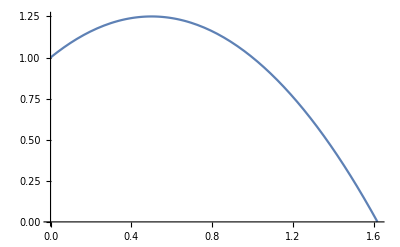

```mathematica
Plot[-x^2+x+1,{x,0,(1+√5)/2}]
```